```mathematica
Table[
With[
{g=ReadGrof[k]},
With[
{base=ChromaticPolynomial[g,4]},
Table[
With[{contracted=EdgeContract[g,e]},
{PlanarGraphQ[contracted], ChromaticPolynomial[contracted,4]/base}
],{e,EdgeList[g]}]
]
],
{k,1,50}
]
```

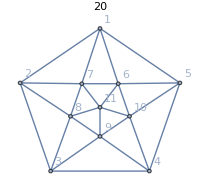
-Graphics-RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0]
RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0]
RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0]
RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0]
RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0]
RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]13

```mathematica
full=Graph[Join[MakeInnerOuterGraph[{0,0,0,0,0}],{7<->11,6<->11,8<->11,9<->11,10<->11}],GraphLayout->"TutteEmbedding"];MyGraph[full,{}]
```

```mathematica
MyGraph[g_,h_]:=Row[{Graph[g,PlotLabel->ChromaticPolynomial[g,4]/24,VertexLabels->"Name",GraphHighlight->h,ImageSize->200],
With[
{sols=Sort[DeleteDuplicates[Map[{x3,x4,x5}/.#&,ToVarsLogical[g,x1==1&&x2==2&&(x3==1||x3==3)]]]]},
Labeled[TableForm[Map[ListToColor, sols],TableSpacing->{0, 0}],Style[Length[sols],Bold,Red]]
]}]
```

```mathematica
Document[g_,e_]:=Block[{},{MyGraph[EdgeDelete[g,e],{e[[1]],e[[2]]}],MyGraph[g,e],MyGraph[EdgeContract[g,e],e[[1]]]}]
```

```mathematica
ListToColor[{1,2}]
```

{RGBColor[1, 0, 0],RGBColor[0, 1, 0]}

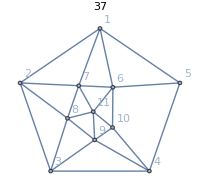
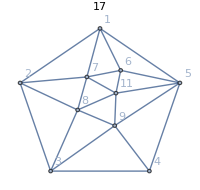
{-Graphics-RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0]
RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0]
RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0]
RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0]
RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0]
RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]13,-Graphics-RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0]
RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0]
RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0]
RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0]
RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0]
RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]13,-Graphics-RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0]
RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0]
RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0]
RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0]
RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]10}

```mathematica
Document[full,5<->10]
```

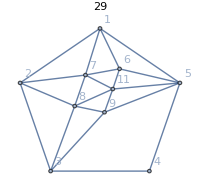
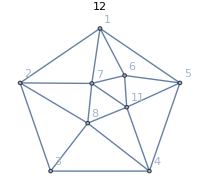
{-Graphics-RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0]
RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0]
RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0]
RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0]
RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0]
RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]11,-Graphics-RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0]
RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0]
RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0]
RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0]
RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]10,-Graphics-RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0]
RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0]
RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0]
RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0]
RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]10}

```mathematica
Document[EdgeContract[full,5<->10],4<->9]
```

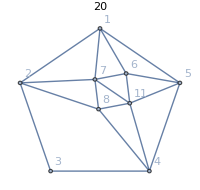
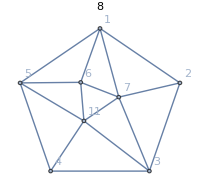
{-Graphics-RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0]
RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0]
RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0]
RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0]
RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0]
RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]12,-Graphics-RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0]
RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0]
RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0]
RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0]
RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]10,-Graphics-RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0]
RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0]
RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0]
RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0]
RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]9}

```mathematica
Document[EdgeContract[EdgeContract[full,5<->10],4<->9],3<->8]
```

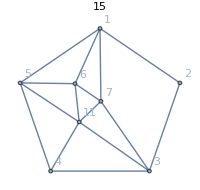
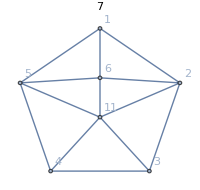
{-Graphics-RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0]
RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0]
RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0]
RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0]
RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0]
RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]12,-Graphics-RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0]
RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[1, 1, 0]
RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[1, 1, 0]
RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0]
RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]9,-Graphics-RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0]
RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]
RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0]
RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]7}

```mathematica
Document[EdgeContract[EdgeContract[EdgeContract[full,5<->10],4<->9],3<->8],2<->7]
```

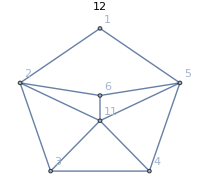
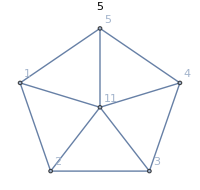
{-Graphics-RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0]
RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0]
RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0]
RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]10,-Graphics-RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0]
RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]
RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0]
RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
RGBColor[0, 0, 1] | RGBColor[1, 1, 0] | RGBColor[0, 0, 1]7,-Graphics-RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]
RGBColor[1, 0, 0] | RGBColor[0, 1, 0] | RGBColor[1, 1, 0]
RGBColor[1, 0, 0] | RGBColor[0, 0, 1] | RGBColor[0, 1, 0]
RGBColor[1, 0, 0] | RGBColor[1, 1, 0] | RGBColor[0, 1, 0]
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 1, 0]
RGBColor[0, 0, 1] | RGBColor[1, 0, 0] | RGBColor[0, 0, 1]
RGBColor[0, 0, 1] | RGBColor[0, 1, 0] | RGBColor[0, 0, 1]7}

```mathematica
Document[EdgeContract[EdgeContract[EdgeContract[EdgeContract[full,5<->10],4<->9],3<->8],2<->7],1<->6]
```